```mathematica
Solve[x^3-3x^2+x-3==0, x, Reals]
```

{{x→3}}

```mathematica
NSolve[x^5+2x==1, x, Reals, WorkingPrecision->10]
```

{{x→0.4863890359}}

```mathematica
f[x_]:=(x^3-5x^2+3x+1)/(2x^2+x-1)
```

```mathematica
g[x_]:=Log[(x^2-1)/(2x-3)]
```

```mathematica
h[x_]:= Sin[x/3]-Cos[x^3/5]
```

```mathematica
f[x]
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x]
```

Log[(-1+x^2)/(-3+2 x)]

```mathematica
h[x]
```

-Cos[x^3/5]+Sin[x/3]

```mathematica
Solve[√f[x]==0, x, Reals]
```

{{x→1},{x→2-√5},{x→2+√5}}

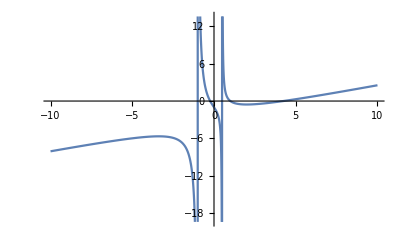

```mathematica
Plot[f[x],{x, -10, 10}]
```

```mathematica
Reduce[f[x]>0,x]
```

-1<x<2-√5||1/2<x<1||x>2+√5

```mathematica
f'[x]
```

(3-10 x+3 x^2)/(-1+x+2 x^2)-((1+4 x) (1+3 x-5 x^2+x^3))/((-1+x+2 x^2)^2)

```mathematica
Reduce[f'[x]>0,x, Reals]
```

x<Root[1-#1+3 #1^2+#1^3&,1]||x>2

```mathematica
N[%]
```

x<-3.38298||x>2.

```mathematica
Solve[g'[x] == 0, x, Reals]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

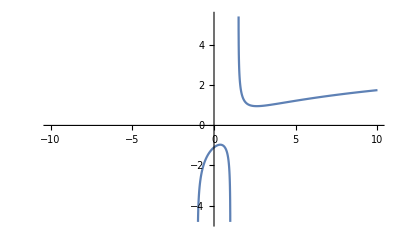

```mathematica
Plot[g[x],{x, -10, 10}]
```

```mathematica
Simplify[g[1/2(3-5^(1/2))]]
```

Log[1/2 (3-√5)]

```mathematica
Simplify[g[1/2(3+5^(1/2))]]
```

Log[1/2 (3+√5)]

```mathematica
g[0]+g'[0]*(x-0)
```

(2 x)/3-Log[3]

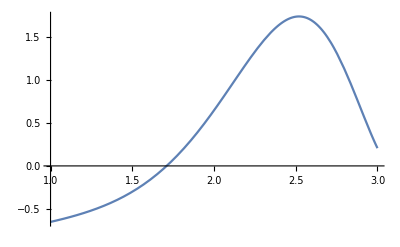

```mathematica
Plot[h[x],{x, 1, 3}]
```

```mathematica
FindRoot[h'[x]== 0,{x,1,3}, WorkingPrecision->10]
```

{x→2.519849497}

```mathematica
h[2.51984949697892514138388166665989323358`10]
```

1.742902764